```mathematica
Print["Solve the ODE for eta, without and with the BC at the origin"]
$Assumptions =a>0;
DSolve[η''[z]==1/(4z^2)(8λ*z^2+2a^2*z^4+3)η[z],η[z],z]
DSolve[{η''[z]==1/(4z^2)(8λ*z^2+2a^2*z^4+3)η[z],η[0]==0},η[z],z]
```

Solve the ODE for eta, without and with the BC at the origin

{{η[z]→(ⅇ^(-z^2/(2 √2)) C[1] HypergeometricU[λ/(√2),0,z^2/(√2)])/(√z)+(ⅇ^(-z^2/(2 √2)) C[2] LaguerreL[-λ/(√2),-1,z^2/(√2)])/(√z)}}

DSolve::bvsing: Unable to resolve some of the arbitrary constants in the general solution using the given boundary conditions. It is possible that some of the conditions have been specified at a singular point for the equation.

{{η[z]→(ⅇ^(-z^2/(2 √2)) C[2] LaguerreL[-λ/(√2),-1,z^2/(√2)])/(√z)}}

```mathematica
Print["Simplify the expression for the eigefunctions"]
η[z_,λ_,a_]:=1/(√z)ⅇ^(-(a *z^2)/(2 √2)) Activate[MeijerGReduce[LaguerreL[-λ/(√2 a),-1,(a *z^2)/(√2)],z]]//FullSimplify
η[z,λ,a]
m[x_,a_]:=2/(x*a^2)Exp[(2 √2)/a x]
s[x_,a_]:=Exp[-(2 √2)/a x]
σ[x_,a_]:=a*√x
p[x_,a_]:=2(√x)/a
$Assumptions=x>=0&&a>0;
ψ[x_,λ_,a_]:=η[p[x,a],λ,a]*√(s[x,a]*σ[x,a])//FullSimplify
ψ[x,λ,a]
```

Simplify the expression for the eigefunctions

-(ⅇ^(-z^2/(2 √2)) z^(3/2) Hypergeometric1F1[1+λ/(√2),2,z^2/(√2)])/(√2)

-2 x Hypergeometric1F1[1-λ/(√2),2,-2 √2 x]

```mathematica
Print["Compute the eigenvalues"]
L0=1;
a0=1;
n=0;
nroots=13;
delta=1;
l=-delta;
r=0;
tol=10^(-6);
f[λ_]:=Hypergeometric1F1[1-λ/(√2 a0),2,-(2 √2 L0)/a0]
eigenvalues={};
While[n<nroots,
temp=Quiet[FindRoot[ f[λ],{λ,0.5*(l+r),l,r}][[1]][[2]]];
If[Abs[f[temp]]<tol,
	AppendTo[eigenvalues,temp];
	n=n+1;
	r=temp-delta;
	l=temp-2*delta,
	l=l-delta];
];
Print[eigenvalues]
Print["Compute the normalization constants"]
cvalues={};
For[k=0,k<nroots,k=k+1;AppendTo[cvalues,NIntegrate[x*Exp[(2 √2*x)/a0]*(Hypergeometric1F1[1-eigenvalues[[k]]/(√2 a0),2,-(2 √2 x)/a0])^2,{x,0,L0}]]];
Print[cvalues]
```

Compute the eigenvalues

{-2.16096,-6.48742,-13.2721,-22.5243,-34.2441,-48.4315,-65.0863,-84.2086,-105.798,-129.855,-156.38,-185.372,-216.831}

Compute the normalization constants

{0.0370655,0.00694171,0.00234917,0.00105847,0.000563589,0.000334731,0.000214721,0.000145845,0.000103533,0.0000761232,0.0000575926,0.0000446191,0.0000352665}

Plot the first 4 eigenfunctions

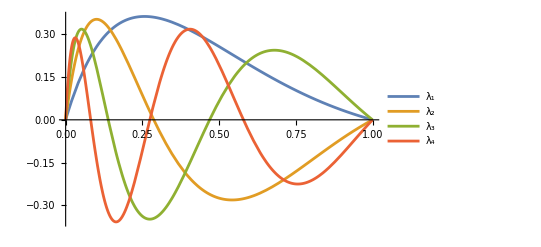

```mathematica
normeigenfun[x_,k_]:=Sqrt[a0/(2*cvalues[[k]])]*x Hypergeometric1F1[1-eigenvalues[[k]]/(√2 a0),2,-(2 √2 x)/a0]
Print["Plot the first 4 eigenfunctions"]
Plot[{normeigenfun[x,1],normeigenfun[x,2],normeigenfun[x,3],normeigenfun[x,4]}, {x,0,L0}, 
PlotLegends->{
Text[Style[ToExpression["\\lambda_1",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\lambda_2",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\lambda_3",TeXForm,HoldForm]]],
Text[Style[ToExpression["\\lambda_4",TeXForm,HoldForm]]]
}]
```

Plotting the density function

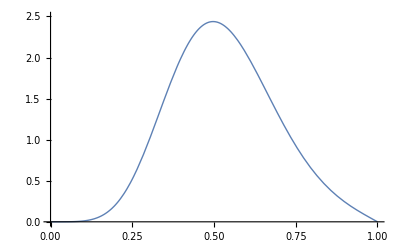
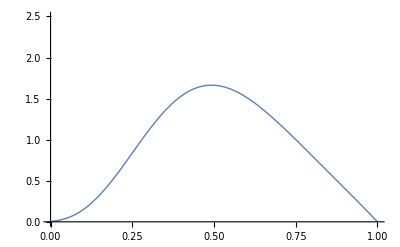
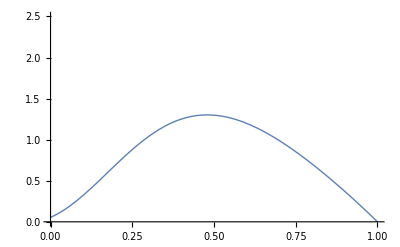
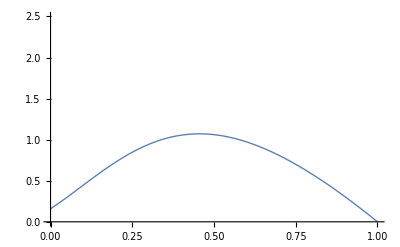
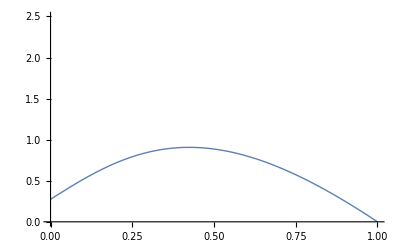
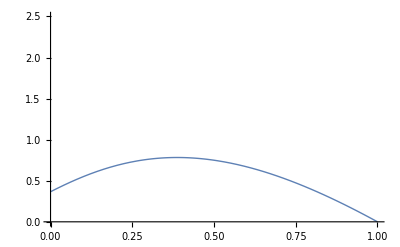

```mathematica
Γ[t_, x_, T_, y_] :=Exp[(2 √2)/a0 y]∑_(k=1)^nroots Exp[eigenvalues[[k]]*(T-t)]/cvalues[[k]] x*Hypergeometric1F1[1-eigenvalues[[k]]/(√2 a0),2,-(2 √2 x)/a0]Hypergeometric1F1[1-eigenvalues[[k]]/(√2 a0),2,-(2 √2 y)/a0]  
Print["Plotting the density function"]
xplot = 0.5*L0;
tplot = 0;
u[y_,T_] := Γ[tplot, xplot, T,y];
plots=Table[Plot[u[y, T],{y, 0, L0}, PlotRange->{-0.001,2.5}, PlotStyle->{Thick}],{T,0.05,0.3, 0.05}]
```

```mathematica
NIntegrate[Γ[tplot, xplot, 0.2,y],{y,0,1}]
```

0.702912

```mathematica
Print["Compute the bond price"]
f[x_,a_]:=-1/a √2 x
v[t_,x_,T_,a_]:=Exp[-x*(T-t)+f[x,a]]
q[t_, x_, T_,a_]:=D[v[t,x,T,a],t]+a √2*x*D[v[t,x,T,a],x] +1/2 a^2 * x *D[D[v[t,x,T,a],x],x]//FullSimplify
q[t,x,T,a]
expr=Integrate[Exp[λ*(s-t)]*q[s,ξ,T,a],{s,t,T}] ;
Print[expr]
TeXForm[expr]
```

Compute the bond price

1/2 a^2 ⅇ^(-(((√2)/a-t+T) x)) (t-T)^2 x

(a^2 ⅇ^(-(((√2)/a-t+T) ξ)) ξ (-2+2 ⅇ^((-t+T) (λ+ξ))-(t-T) (λ+ξ) (-2+(t-T) (λ+ξ))))/(2 (λ+ξ)^3)

\frac{a^2 \xi  e^{-\left(\xi  \left(\frac{\sqrt{2}}{a}-t+T\right)\right)} \left(-((\lambda +\xi ) (t-T) ((\lambda +\xi ) (t-T)-2))+2
   e^{(\lambda +\xi ) (T-t)}-2\right)}{2 (\lambda +\xi )^3}

```mathematica
h[t_,T_,ξ_,λ_,a_]:=(a^2 ⅇ^(((√2)/a-(T-t)) ξ) ξ (-2+2 ⅇ^((-t+T) (λ+ξ))-(t-T) (λ+ξ) (-2+(t-T) (λ+ξ))))/(2 (λ+ξ)^3)
fun[x_,k_]:=Hypergeometric1F1[1-eigenvalues[[k]]/(√2 a0),2,-(2 √2 x)/a0]
B[x_,t_,T_]:=Exp[-x*(T-t)]+x*Exp[(√2)/a0 x]*NIntegrate[∑_(k=1)^nroots (fun[x,k]/cvalues[[k]] h[t,T,ξ,eigenvalues[[k]],a0]*fun[ξ,k]) ,{ξ,0,L0}]
```

1/3

1/2

2/3

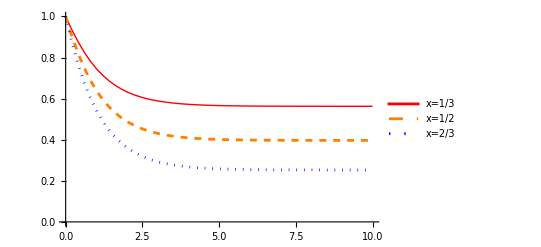

```mathematica
Print["1/3"]
p1=Plot[B[1/3*L0,0,T],{T,0,10},PlotPoints->50,MaxRecursion->0, PlotRange->{0,1}, PlotStyle->{Red,Thick},PlotLegends->{Text[Style[HoldForm[x=1/3]]]}];
Print["1/2"]
p2=Plot[B[1/2*L0,0,T],{T,0,10},PlotPoints->50,MaxRecursion->0, PlotRange->{0,1}, PlotStyle->{Orange,Dashed},
PlotLegends->{Text[Style[HoldForm[x=1/2]]]}];
Print["2/3"]
p3=Plot[B[2/3*L0,0,T],{T,0,10},PlotPoints->50,MaxRecursion->0, PlotRange->{0,1}, PlotStyle->{Blue,Dotted},PlotLegends->{Text[Style[HoldForm[x=2/3]]]}];
Show[p1, p2, p3]
```

1/3

1/2

2/3

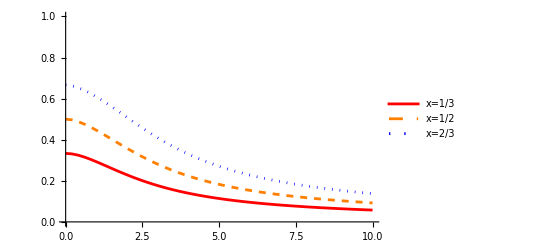

```mathematica
Y[x_,t_, T_] := -1/T Log[B[x,t,T]]
Print["1/3"]
p1=Plot[Y[1/3 * L0,0,T],{T,0,10},PlotPoints->50,MaxRecursion->0, PlotRange->{0,L0}, PlotStyle->{Red,Thick},PlotLegends->{Text[Style[HoldForm[x=1/3]]]}];
Print["1/2"]
p2=Plot[Y[1/2 * L0,0,T],{T,0,10},PlotPoints->50,MaxRecursion->0, PlotRange->{0,L0}, PlotStyle->{Orange,Dashed},PlotLegends->{Text[Style[HoldForm[x=1/2]]]}];
Print["2/3"]
p3=Plot[Y[2/3 * L0,0,T],{T,0,10},PlotPoints->50,MaxRecursion->0, PlotRange->{0,L0}, PlotStyle->{Blue,Dotted},PlotLegends->{Text[Style[HoldForm[x=2/3]]]}];
Show[p1, p2, p3]
```